```mathematica
Сначала находим основное решение
```

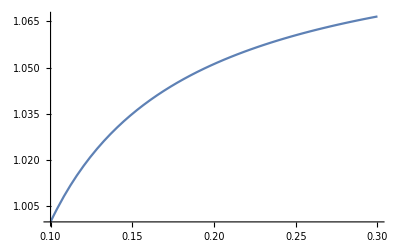

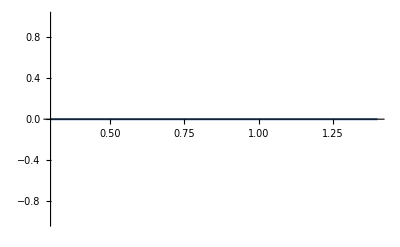

```mathematica
γ=2.0;
r1=0.3;
F=0.0;
s=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F*u[r]/ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]*u[r]/ρ[r],u[0.1]==1,ρ[0.1]==1,p[0.1]==0.05},{ρ,u,p},{r,0.1,r1}];
Plot[u[x]/. s,{x, 0.1,r1}]
DD = 0;
ro1 =ρ[r1]/. s[[1]];
pp1 = p[r1]/. s[[1]];
uu1 = u[r1]/. s[[1]];
F=0.0;
g = 2.0;
ss = NSolve[ro1*(uu1-DD)==ro*(u-DD)&&ro1*uu1*(uu1 - DD) + pp1 == ro*u*(u - DD)+ p&& ro1*(uu1 - DD)*(pp1/(ro1*(g-1)) + uu1^2/2) + pp1 * uu1==ro*(u - DD)*(p/(ro*(g-1)) + (u^2)/2) + p * u ,{ro, u, p},Reals];
g1=u/. ss[[1]];
g2=ro/. ss[[1]];
g3=p/. ss[[1]];
r2=1.4;
sss=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F*u[r]/ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]u[r]/ρ[r],u[r1]==g1,ρ[r1]==g2,p[r1]==g3},{ρ,u,p},{r,r1,r2}];
sss=NDSolve[{ρ'[r]==0, u'[r]==0,p'[r]==0,u[r1]==0,ρ[r1]==g2,p[r1]==g3},{ρ,u,p},{r,r1,r2}];
Plot[u[x]/. sss,{x, r1, r2}]
```

```mathematica
РЕШАЕМ ЛИНЕЙНУЮ ЗАДАЧУ
```

```mathematica
(*Простая функция линеаризации*)
LinearizeSingleEquation[eq_,baseVars_,pertVars_,eps_]:=Module[{},Coefficient[Normal[Series[eq,{eps,0,1}]],eps]];

(*Пример использования*)
u=u0[r]+ε*u1[r,ϕ,t];
v=v0[r]+ε*v1[r,ϕ,t];
ρ=ρ0[r]+ε*ρ1[r,ϕ,t];
p=p0[r]+ε*p1[r,ϕ,t];

(*Уравнение 1*)
eq1=D[ρ,t]+D[r*ρ*u,r]/r+D[ρ*v,ϕ]/r;
result1=LinearizeSingleEquation[eq1,{u0,v0,ρ0,p0},{u1,v1,ρ1,p1},ε]*r;

(*Уравнение 2*)
eq2=D[ρ*u,t]+D[r*(ρ*u*u+p),r]/r+D[ρ*u*v,ϕ]/r-ρ*v*v/r-p/r+F*u/ρ;
result2=LinearizeSingleEquation[eq2,{u0,v0,ρ0,p0},{u1,v1,ρ1,p1},ε]*r;

(*Уравнение 3*)
eq3=D[ρ*v,t]+D[r*ρ*u*v,r]/r+D[ρ*v*v+p,ϕ]/r+ρ*u*v/r+F*v/ρ;
result3=LinearizeSingleEquation[eq3,{u0,v0,ρ0,p0},{u1,v1,ρ1,p1},ε]*r;

(*Уравнение 4*)
eq4=D[p/(γ-1) + ρ*(u*u+v*v)/2,t]+D[r*u*(γ*p/(γ-1) + ρ*(u*u+v*v)/2),r]/r+D[v*(γ*p/(γ-1) + ρ*(u*u+v*v)/2),ϕ]/r+F*(u*u+v*v)/ρ;
result4=LinearizeSingleEquation[eq4,{u0,v0,ρ0,p0},{u1,v1,ρ1,p1},ε]*r;

Print["Результаты:"];
Print["Ур1: ",Simplify[result1]];
Print["Ур2: ",Simplify[result2]];
Print["Ур3: ",Simplify[result3]];
Print["Ур4: ",Simplify[result4]];
```

Результаты:

Ур1: r ρ1[r,ϕ,t] u0'[r]+u1[r,ϕ,t] (ρ0[r]+r ρ0'[r])+r ρ1^(0,0,1)[r,ϕ,t]+ρ0[r] v1^(0,1,0)[r,ϕ,t]+v0[r] ρ1^(0,1,0)[r,ϕ,t]+r ρ0[r] u1^(1,0,0)[r,ϕ,t]+u0[r] (ρ1[r,ϕ,t]+r ρ1^(1,0,0)[r,ϕ,t])

Ур2: -v0[r]^2 ρ1[r,ϕ,t]+v0[r] ρ0[r] (-2 v1[r,ϕ,t]+u1^(0,1,0)[r,ϕ,t])+r (2 u1[r,ϕ,t] ρ0[r] u0'[r]+ρ0[r] u1^(0,0,1)[r,ϕ,t]+p1^(1,0,0)[r,ϕ,t])+u0[r] (2 r ρ1[r,ϕ,t] u0'[r]+2 u1[r,ϕ,t] (ρ0[r]+r ρ0'[r])+r ρ1^(0,0,1)[r,ϕ,t]+ρ0[r] v1^(0,1,0)[r,ϕ,t]+v0[r] ρ1^(0,1,0)[r,ϕ,t]+2 r ρ0[r] u1^(1,0,0)[r,ϕ,t])+u0[r]^2 (ρ1[r,ϕ,t]+r ρ1^(1,0,0)[r,ϕ,t])

Ур3: r v1[r,ϕ,t] ρ0[r] u0'[r]+r v0[r] ρ1[r,ϕ,t] u0'[r]+u1[r,ϕ,t] (r ρ0[r] v0'[r]+v0[r] (2 ρ0[r]+r ρ0'[r]))+r ρ0[r] v1^(0,0,1)[r,ϕ,t]+r v0[r] ρ1^(0,0,1)[r,ϕ,t]+p1^(0,1,0)[r,ϕ,t]+2 v0[r] ρ0[r] v1^(0,1,0)[r,ϕ,t]+v0[r]^2 ρ1^(0,1,0)[r,ϕ,t]+r v0[r] ρ0[r] u1^(1,0,0)[r,ϕ,t]+u0[r] (2 v0[r] ρ1[r,ϕ,t]+r ρ1[r,ϕ,t] v0'[r]+v1[r,ϕ,t] (2 ρ0[r]+r ρ0'[r])+r ρ0[r] v1^(1,0,0)[r,ϕ,t]+r v0[r] ρ1^(1,0,0)[r,ϕ,t])

Ур4: 1.5 u0[r]^2 u1[r,ϕ,t] ρ0[r]+0.5 u1[r,ϕ,t] v0[r]^2 ρ0[r]+1. u0[r] v0[r] v1[r,ϕ,t] ρ0[r]+0.5 u0[r]^3 ρ1[r,ϕ,t]+0.5 u0[r] v0[r]^2 ρ1[r,ϕ,t]+2. r u1[r,ϕ,t] p0'[r]+3. r u0[r] u1[r,ϕ,t] ρ0[r] u0'[r]+1. r v0[r] v1[r,ϕ,t] ρ0[r] u0'[r]+1.5 r u0[r]^2 ρ1[r,ϕ,t] u0'[r]+0.5 r v0[r]^2 ρ1[r,ϕ,t] u0'[r]+p1[r,ϕ,t] (2. u0[r]+2. r u0'[r])+1. r u1[r,ϕ,t] v0[r] ρ0[r] v0'[r]+1. r u0[r] v1[r,ϕ,t] ρ0[r] v0'[r]+1. r u0[r] v0[r] ρ1[r,ϕ,t] v0'[r]+1.5 r u0[r]^2 u1[r,ϕ,t] ρ0'[r]+0.5 r u1[r,ϕ,t] v0[r]^2 ρ0'[r]+1. r u0[r] v0[r] v1[r,ϕ,t] ρ0'[r]+1. r p1^(0,0,1)[r,ϕ,t]+r u0[r] ρ0[r] u1^(0,0,1)[r,ϕ,t]+r v0[r] ρ0[r] v1^(0,0,1)[r,ϕ,t]+1/2 r u0[r]^2 ρ1^(0,0,1)[r,ϕ,t]+1/2 r v0[r]^2 ρ1^(0,0,1)[r,ϕ,t]+2. v0[r] p1^(0,1,0)[r,ϕ,t]+1. u0[r] v0[r] ρ0[r] u1^(0,1,0)[r,ϕ,t]+0.5 u0[r]^2 ρ0[r] v1^(0,1,0)[r,ϕ,t]+1.5 v0[r]^2 ρ0[r] v1^(0,1,0)[r,ϕ,t]+0.5 u0[r]^2 v0[r] ρ1^(0,1,0)[r,ϕ,t]+0.5 v0[r]^3 ρ1^(0,1,0)[r,ϕ,t]+2. r u0[r] p1^(1,0,0)[r,ϕ,t]+1.5 r u0[r]^2 ρ0[r] u1^(1,0,0)[r,ϕ,t]+0.5 r v0[r]^2 ρ0[r] u1^(1,0,0)[r,ϕ,t]+p0[r] (2. u1[r,ϕ,t]+2. v1^(0,1,0)[r,ϕ,t]+2. r u1^(1,0,0)[r,ϕ,t])+1. r u0[r] v0[r] ρ0[r] v1^(1,0,0)[r,ϕ,t]+0.5 r u0[r]^3 ρ1^(1,0,0)[r,ϕ,t]+0.5 r u0[r] v0[r]^2 ρ1^(1,0,0)[r,ϕ,t]

```mathematica
eqv1 = r ρ1[r,ϕ,t] u0'[r]+u1[r,ϕ,t] (ρ0[r]+r ρ0'[r])+r Derivative[0,0,1][ρ1][r,ϕ,t]+ρ0[r] Derivative[0,1,0][v1][r,ϕ,t]+v0[r] Derivative[0,1,0][ρ1][r,ϕ,t]+r ρ0[r] Derivative[1,0,0][u1][r,ϕ,t]+u0[r] (ρ1[r,ϕ,t]+r Derivative[1,0,0][ρ1][r,ϕ,t]);
eqv2 =u0[r]^2 ρ1[r,ϕ,t]-v0[r]^2 ρ1[r,ϕ,t]-(F r u0[r] ρ1[r,ϕ,t])/ρ0[r]^2+2 r u0[r] ρ1[r,ϕ,t] u0'[r]+u1[r,ϕ,t] ((F r)/ρ0[r]+2 ρ0[r] (u0[r]+r u0'[r])+2 r u0[r] ρ0'[r])+r ρ0[r] Derivative[0,0,1][u1][r,ϕ,t]+r u0[r] Derivative[0,0,1][ρ1][r,ϕ,t]+u0[r] ρ0[r] Derivative[0,1,0][v1][r,ϕ,t]+v0[r] (-2 v1[r,ϕ,t] ρ0[r]+ρ0[r] Derivative[0,1,0][u1][r,ϕ,t]+u0[r] Derivative[0,1,0][ρ1][r,ϕ,t])+r Derivative[1,0,0][p1][r,ϕ,t]+2 r u0[r] ρ0[r] Derivative[1,0,0][u1][r,ϕ,t]+r u0[r]^2 Derivative[1,0,0][ρ1][r,ϕ,t];eqv3 =2 u0[r] v0[r] ρ1[r,ϕ,t]-(F r v0[r] ρ1[r,ϕ,t])/ρ0[r]^2+r v0[r] ρ1[r,ϕ,t] u0'[r]+r u0[r] ρ1[r,ϕ,t] v0'[r]+v1[r,ϕ,t] ((F r)/ρ0[r]+ρ0[r] (2 u0[r]+r u0'[r])+r u0[r] ρ0'[r])+u1[r,ϕ,t] (2 v0[r] ρ0[r]+r ρ0[r] v0'[r]+r v0[r] ρ0'[r])+r ρ0[r] Derivative[0,0,1][v1][r,ϕ,t]+r v0[r] Derivative[0,0,1][ρ1][r,ϕ,t]+Derivative[0,1,0][p1][r,ϕ,t]+2 v0[r] ρ0[r] Derivative[0,1,0][v1][r,ϕ,t]+v0[r]^2 Derivative[0,1,0][ρ1][r,ϕ,t]+r v0[r] ρ0[r] Derivative[1,0,0][u1][r,ϕ,t]+r u0[r] ρ0[r] Derivative[1,0,0][v1][r,ϕ,t]+r u0[r] v0[r] Derivative[1,0,0][ρ1][r,ϕ,t];eqv4 =u1[r,ϕ,t] ((γ p0[r])/(-1+γ)+1/2 (u0[r]^2+v0[r]^2) ρ0[r])+(F r (2 (u0[r] u1[r,ϕ,t]+v0[r] v1[r,ϕ,t]) ρ0[r]-(u0[r]^2+v0[r]^2) ρ1[r,ϕ,t]))/ρ0[r]^2+u0[r] ((γ p1[r,ϕ,t])/(-1+γ)+(u0[r] u1[r,ϕ,t]+v0[r] v1[r,ϕ,t]) ρ0[r]+1/2 (u0[r]^2+v0[r]^2) ρ1[r,ϕ,t])+(r Derivative[0,0,1][p1][r,ϕ,t])/(-1+γ)+r ρ0[r] (u0[r] Derivative[0,0,1][u1][r,ϕ,t]+v0[r] Derivative[0,0,1][v1][r,ϕ,t])+1/2 r (u0[r]^2+v0[r]^2) Derivative[0,0,1][ρ1][r,ϕ,t]+((γ p0[r])/(-1+γ)+1/2 (u0[r]^2+v0[r]^2) ρ0[r]) Derivative[0,1,0][v1][r,ϕ,t]+v0[r] ((γ Derivative[0,1,0][p1][r,ϕ,t])/(-1+γ)+ρ0[r] (u0[r] Derivative[0,1,0][u1][r,ϕ,t]+v0[r] Derivative[0,1,0][v1][r,ϕ,t])+1/2 (u0[r]^2+v0[r]^2) Derivative[0,1,0][ρ1][r,ϕ,t])+r (((γ p1[r,ϕ,t])/(-1+γ)+(u0[r] u1[r,ϕ,t]+v0[r] v1[r,ϕ,t]) ρ0[r]+1/2 (u0[r]^2+v0[r]^2) ρ1[r,ϕ,t]) u0'[r]+((γ p0[r])/(-1+γ)+1/2 (u0[r]^2+v0[r]^2) ρ0[r]) Derivative[1,0,0][u1][r,ϕ,t])+r (u1[r,ϕ,t] ((γ p0'[r])/(-1+γ)+ρ0[r] (u0[r] u0'[r]+v0[r] v0'[r])+1/2 (u0[r]^2+v0[r]^2) ρ0'[r])+u0[r] (u1[r,ϕ,t] ρ0[r] u0'[r]+u0[r] ρ1[r,ϕ,t] u0'[r]+v1[r,ϕ,t] ρ0[r] v0'[r]+v0[r] ρ1[r,ϕ,t] v0'[r]+(u0[r] u1[r,ϕ,t]+v0[r] v1[r,ϕ,t]) ρ0'[r]+(γ Derivative[1,0,0][p1][r,ϕ,t])/(-1+γ)+u0[r] ρ0[r] Derivative[1,0,0][u1][r,ϕ,t]+v0[r] ρ0[r] Derivative[1,0,0][v1][r,ϕ,t]+1/2 (u0[r]^2+v0[r]^2) Derivative[1,0,0][ρ1][r,ϕ,t]));
```

```mathematica
u1[r_,ϕ_,t_]:=U[r]*Exp[ⅈ*(m * ϕ-ω*t)];
v1[r_,ϕ_,t_]:=V[r]*Exp[ⅈ*(m * ϕ-ω*t)];
ρ1[r_,ϕ_,t_]:=R[r]*Exp[ⅈ*(m * ϕ-ω*t)];
p1[r_,ϕ_,t_]:=P[r]*Exp[ⅈ*(m * ϕ-ω*t)];
ξ[ϕ_,t_]:=Xi*Exp[ⅈ*(m * ϕ-ω*t)];
```

```mathematica
eqv1 /(ⅇ^(ⅈ (m ϕ-t ω)) )//FullSimplify
eqv2/(ⅇ^(ⅈ (m ϕ-t ω)) )//FullSimplify
eqv3/(ⅇ^(ⅈ (m ϕ-t ω)) )//FullSimplify
eqv4 /(ⅇ^(ⅈ (m ϕ-t ω)) )//FullSimplify
```

r u0[r] R'[r]+ρ0[r] (U[r]+ⅈ m V[r]+r U'[r])+R[r] (-ⅈ r ω+u0[r]+ⅈ m v0[r]+r u0'[r])+r U[r] ρ0'[r]

ⅈ m u0[r] V[r] ρ0[r]-2 V[r] v0[r] ρ0[r]+r P'[r]+r u0[r]^2 R'[r]+2 r u0[r] ρ0[r] U'[r]+R[r] (u0[r]^2-v0[r]^2+u0[r] (-ⅈ r ω+ⅈ m v0[r]+2 r u0'[r]))+U[r] (ρ0[r] (-ⅈ r ω+2 u0[r]+ⅈ m v0[r]+2 r u0'[r])+2 r u0[r] ρ0'[r])

ⅈ m P[r]+2 U[r] v0[r] ρ0[r]+2 ⅈ m V[r] v0[r] ρ0[r]+(-ⅈ r ω+2 u0[r]) (R[r] v0[r]+V[r] ρ0[r])+r u0[r] v0[r] R'[r]+r v0[r] ρ0[r] U'[r]+r V[r] ρ0[r] u0'[r]+r u0[r] ρ0[r] V'[r]+r U[r] ρ0[r] v0'[r]+R[r] (ⅈ m v0[r]^2+r v0[r] u0'[r]+r u0[r] v0'[r])+r (u0[r] V[r]+U[r] v0[r]) ρ0'[r]

(1.+0. ⅈ) (p0[r] (2. U[r]+(0.+2. ⅈ) m V[r])-(0.+1. ⅈ) r ω U[r] u0[r] ρ0[r]+1.5 U[r] u0[r]^2 ρ0[r]+(0.+0.5 ⅈ) m u0[r]^2 V[r] ρ0[r]+(0.+1. ⅈ) m U[r] u0[r] v0[r] ρ0[r]-(0.+1. ⅈ) r ω V[r] v0[r] ρ0[r]+1. u0[r] V[r] v0[r] ρ0[r]+0.5 U[r] v0[r]^2 ρ0[r]+(0.+1.5 ⅈ) m V[r] v0[r]^2 ρ0[r]+2. r u0[r] P'[r]+2. r U[r] p0'[r]+0.5 r u0[r]^3 R'[r]+0.5 r u0[r] v0[r]^2 R'[r]+2. r p0[r] U'[r]+1.5 r u0[r]^2 ρ0[r] U'[r]+0.5 r v0[r]^2 ρ0[r] U'[r]+3. r U[r] u0[r] ρ0[r] u0'[r]+1. r V[r] v0[r] ρ0[r] u0'[r]+P[r] ((0.-1. ⅈ) r ω+2. u0[r]+(0.+2. ⅈ) m v0[r]+2. r u0'[r])+1. r u0[r] v0[r] ρ0[r] V'[r]+1. r u0[r] V[r] ρ0[r] v0'[r]+1. r U[r] v0[r] ρ0[r] v0'[r]+R[r] (0.5 u0[r]^3+v0[r]^2 ((0.-0.5 ⅈ) r ω+(0.+0.5 ⅈ) m v0[r]+0.5 r u0'[r])+u0[r]^2 ((0.-0.5 ⅈ) r ω+(0.+0.5 ⅈ) m v0[r]+1.5 r u0'[r])+u0[r] v0[r] (0.5 v0[r]+1. r v0'[r]))+r (1. u0[r] V[r] v0[r]+U[r] (1.5 u0[r]^2+0.5 v0[r]^2)) ρ0'[r])

```mathematica
yr1[r_]:=r u0[r] R'[r]+ρ0[r] (U[r]+ⅈ m V[r]+r U'[r])+R[r] (-ⅈ r ω+u0[r]+ⅈ m v0[r]+r u0'[r])+r U[r] ρ0'[r];
yr2[r_]:=1/ρ0[r]^2(R[r] (u0[r]^2 ρ0[r]^2-v0[r]^2 ρ0[r]^2+u0[r] (-F r+ρ0[r]^2 (-ⅈ r ω+ⅈ m v0[r]+2 r u0'[r])))+ρ0[r] (ρ0[r] (-2 V[r] v0[r] ρ0[r]+r P'[r]+r u0[r]^2 R'[r]+u0[r] ρ0[r] (ⅈ m V[r]+2 r U'[r]))+U[r] (F r+ρ0[r]^2 (-ⅈ r ω+2 u0[r]+ⅈ m v0[r]+2 r u0'[r])+2 r u0[r] ρ0[r] ρ0'[r])));
yr3[r_]:=1/ρ0[r]^2(R[r] (v0[r] (-F r+ρ0[r]^2 (-ⅈ r ω+2 u0[r]+ⅈ m v0[r]+r u0'[r]))+r u0[r] ρ0[r]^2 v0'[r])+ρ0[r] (V[r] (F r+ρ0[r]^2 (-ⅈ r ω+2 u0[r]+2 ⅈ m v0[r]+r u0'[r])+r u0[r] ρ0[r] ρ0'[r])+ρ0[r] (ⅈ m P[r]+r v0[r] ρ0[r] U'[r]+r u0[r] (v0[r] R'[r]+ρ0[r] V'[r])+r U[r] ρ0[r] v0'[r]+U[r] v0[r] (2 ρ0[r]+r ρ0'[r]))));
yr4[r_]:=1/(2 (-1+γ) ρ0[r]^2)(-((-1+γ) R[r] (-u0[r]^3 ρ0[r]^2+v0[r]^2 (2 F r+ⅈ ρ0[r]^2 (r ω-m v0[r]+ⅈ r u0'[r]))+u0[r]^2 (2 F r+ⅈ ρ0[r]^2 (r ω-m v0[r]+3 ⅈ r u0'[r]))-u0[r] v0[r] ρ0[r]^2 (v0[r]+2 r v0'[r])))+ρ0[r] (ρ0[r] (2 P[r] (-ⅈ r ω+γ (u0[r]+ⅈ m v0[r]+r u0'[r]))+r ((-1+γ) u0[r]^3 R'[r]+3 (-1+γ) u0[r]^2 ρ0[r] U'[r]+(2 γ p0[r]+(-1+γ) v0[r]^2 ρ0[r]) U'[r]+u0[r] (2 γ P'[r]+(-1+γ) v0[r] (v0[r] R'[r]+2 ρ0[r] V'[r]))))+V[r] (3 ⅈ m (-1+γ) v0[r]^2 ρ0[r]^2+ρ0[r] (2 ⅈ m γ p0[r]+(-1+γ) u0[r] ρ0[r] (ⅈ m u0[r]+2 r v0'[r]))+2 (-1+γ) v0[r] (2 F r+ρ0[r]^2 (-ⅈ r ω+u0[r]+r u0'[r])+r u0[r] ρ0[r] ρ0'[r]))+U[r] (2 (-1+γ) u0[r] (2 F r+ρ0[r]^2 (-ⅈ r ω+ⅈ m v0[r]+3 r u0'[r]))+3 (-1+γ) u0[r]^2 ρ0[r] (ρ0[r]+r ρ0'[r])+ρ0[r] (2 γ p0[r]+2 r γ p0'[r]+2 r (-1+γ) v0[r] ρ0[r] v0'[r]+(-1+γ) v0[r]^2 (ρ0[r]+r ρ0'[r])))));
```

```mathematica
F=0;
R1 = 0.3;
R2 = 1.4;
Num=10; (* число точек коллокации внутри области*)
xk[k_]:=R1 + (1+Cos[π*(k-0.5)/Num])/2 * (R2 - R1)//N;
collocationPoints=Table[xk[k],{k,Num}];
equations={yr1,yr2,yr3,yr4};
basis[n_,r_]:=ChebyshevT[n,(2*(r-R1)/(R2-R1))-1];
R[r_]:=Sum[kr[n]*basis[n,r],{n,0,Num }];
U[r_]:=Sum[ku[n]*basis[n,r],{n,0,Num }];
V[r_]:=Sum[kv[n]*basis[n,r],{n,0,Num }];
P[r_]:=Sum[kp[n]*basis[n,r],{n,0,Num }];
variables=Join[Table[kr[i],{i,0,Num }],Table[ku[i],{i,0,Num }],Table[kv[i],{i,0,Num }],Table[kp[i],{i,0,Num }], {Xi}]
nVars=Length[variables];
u0[r_]=u[r]/. sss;
v0[r_]=0.0;
ρ0[r_]=ρ[r]/. sss;
p0[r_]=p[r]/. sss;
```

{kr[0],kr[1],kr[2],kr[3],kr[4],kr[5],kr[6],kr[7],kr[8],kr[9],kr[10],ku[0],ku[1],ku[2],ku[3],ku[4],ku[5],ku[6],ku[7],ku[8],ku[9],ku[10],kv[0],kv[1],kv[2],kv[3],kv[4],kv[5],kv[6],kv[7],kv[8],kv[9],kv[10],kp[0],kp[1],kp[2],kp[3],kp[4],kp[5],kp[6],kp[7],kp[8],kp[9],kp[10],Xi}

```mathematica
collocationPoints
```

{1.39323,1.34005,1.23891,1.09969,0.936039,0.763961,0.600305,0.461091,0.359946,0.306771}

```mathematica
(*Инициализация матриц A и B*)
A={};
B={};
(*Цикл по всем уравнениям и точкам коллокации*)
Do[Do[(*Вычисляем уравнение в текущей точке*)
currentEquation=equations[[eqIndex]][collocationPoints[[pointIndex]]];
(*Разделяем на части с ω и без ω*)
equationWithoutOmega=currentEquation/. ω->0;
equationOmegaPart=currentEquation-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];,
{pointIndex,Length[collocationPoints]}],
{eqIndex,Length[equations]}];
```

```mathematica
Print["Размер матрицы A: ",Dimensions[A]]
Print["Размер матрицы B: ",Dimensions[B]]
Print["Количество уравнений: ",Length[equations]*Length[collocationPoints]]
Print["Количество переменных: ",nVars]
```

Размер матрицы A: {40,45,1}

Размер матрицы B: {40,45,1}

Количество уравнений: 40

Количество переменных: 45

```mathematica
Добавим уравнения на граничные условия
```

```mathematica
(*Жёсткое Правое граничное условие*)
```

```mathematica
boundaryRowA=Table[Coefficient[P[R2],variables[[i]]],{i,nVars}];
boundaryRowB=ConstantArray[0,nVars];
AppendTo[A,boundaryRowA];
AppendTo[B,boundaryRowB];
Print["Размер матрицы A: ",Dimensions[A]]
Print["Размер матрицы B: ",Dimensions[B]]
```

Размер матрицы A: {41,45}

Размер матрицы B: {41,45}

```mathematica
(*Мягкое Правое граничное условие*)
boundaryRowA=Table[Coefficient[D[P[r],r]/. r->R2,variables[[i]]],{i,nVars}];
boundaryRowB=ConstantArray[0,nVars];
AppendTo[A,boundaryRowA];
AppendTo[B,boundaryRowB];
Print["Размер матрицы A: ",Dimensions[A]]
Print["Размер матрицы B: ",Dimensions[B]]
```

Размер матрицы A: {41,45}

Размер матрицы B: {41,45}

```mathematica
(*1 Неотражающее Правое граничное условие*)
boundaryRowA=Table[Coefficient[P[r]-ρ0[r]*Sqrt[γ*p0[r]/ρ0[r]]*U[r]/. r->R2,variables[[i]]],{i,nVars}];
boundaryRowB=ConstantArray[0,nVars];
AppendTo[A,boundaryRowA];
AppendTo[B,boundaryRowB];
Print["Размер матрицы A: ",Dimensions[A]]
Print["Размер матрицы B: ",Dimensions[B]]
```

Размер матрицы A: {41,45,1}

Размер матрицы B: {41,45}

```mathematica
(*2 Неотражающее Правое граничное условие - второй вариант*)
beq1=(p1[R2,ϕ,t]-ρ0[R2]*Sqrt[γ*p0[R2]/ρ0[R2]]*u1[R2,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
equationWithoutOmega=beq1/. ω->0;
equationOmegaPart=beq1-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];
```

```mathematica
(*Левое граничное условие*)
```

```mathematica
beq1=(ρ0[R1]*u1[R1,ϕ,t]+u0[R1]*ρ1[R1,ϕ,t]-ⅈ*ω*ξ[ϕ,t]*(ro1-ρ0[R1]))/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq2=(v1[R1,ϕ,t]-(uu1-u0[R1])*ⅈ*ξ[ϕ,t]/R1)/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq3=(2*ρ0[R1]*u0[R1]*u1[R1,ϕ,t]+u0[R1]*u0[R1]*ρ1[R1,ϕ,t]+p1[R1,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq4=(p1[R1,ϕ,t]-γ*p0[R1]/ρ0[R1] * ρ1[R1,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
```

```mathematica
(*Нулевое Левое граничное условие*)
beq1=(u1[R1,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq2=(ξ[ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq3=(ρ1[R1,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq4=(p1[R1,ϕ,t]-)/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq5=(γ/(γ-1) * (p1[R1,ϕ,t]/ρ0[R1] - p0[R1]*ρ1[R1,ϕ,t]/(ρ0[R1]*ρ0[R1])) + u0[R1]*u1[R1,ϕ,t]+v0[R1]*v1[R1,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
```

```mathematica
equationWithoutOmega=beq1/. ω->0;
equationOmegaPart=beq1-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];

equationWithoutOmega=beq2/. ω->0;
equationOmegaPart=beq2-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];

equationWithoutOmega=beq3/. ω->0;
equationOmegaPart=beq3-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];

equationWithoutOmega=beq4/. ω->0;
equationOmegaPart=beq4-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];
```

```mathematica
Print["Размер матрицы A: ",Dimensions[A]]
Print["Размер матрицы B: ",Dimensions[B]]
```

Размер матрицы A: {45,45}

Размер матрицы B: {45,45}

```mathematica
Aflat=Table[If[Head[A[[i,j]]]===List,A[[i,j,1]],A[[i,j]]],{i,Dimensions[A][[1]]},{j,Dimensions[A][[2]]}];
Bflat=Table[If[Head[B[[i,j]]]===List,B[[i,j,1]],B[[i,j]]],{i,Dimensions[B][[1]]},{j,Dimensions[B][[2]]}];
boundaryIndices=Flatten[Position[Map[Total[Abs[#]]&,Bflat],0]];
interiorIndices=Complement[Range[Dimensions[B][[1]]],boundaryIndices];
Cmatrix=Aflat[[boundaryIndices]];
kernelBasis=NullSpace[Cmatrix];
Print["Размерность подпространства: ",Length[kernelBasis]];
(*4. Строим матрицу проекции V*)
V=Transpose[kernelBasis];  (*Столбцы V-базисные векторы*)
(*5. Проецируем матрицы на подпространство*)
Aproj=Transpose[V].Aflat.V;
Bproj=Transpose[V].Bflat.V;
Print["Размер A_proj: ",Dimensions[Aproj]];
Print["Размер B_proj: ",Dimensions[Bproj]];
```

Размерность подпространства: 30

Размер A_proj: {30,30}

Размер B_proj: {30,30}

```mathematica
mValue=1;  (*например*)
An=N[Aproj/. m->mValue];
Bn=N[Bproj/. m->mValue];
eigenvalues=Eigenvalues[{An,Bn}]
```

{-8.08666×10^-8+1.01191×10^-6 ⅈ,8.08665×10^-8-1.01191×10^-6 ⅈ,-4.30778×10^-15+2.53645×10^-14 ⅈ,1.15159×10^-14+7.042×10^-15 ⅈ,2.94966×10^-15+7.78244×10^-15 ⅈ,-6.79537×10^-15+2.43773×10^-15 ⅈ,6.75325×10^-16-2.65327×10^-15 ⅈ,-1.10676×10^-15-2.03415×10^-15 ⅈ,1.29238×10^-15-1.6566×10^-16 ⅈ,-9.88234×10^-16+4.41284×10^-16 ⅈ,-4.66304×10^-16+5.12341×10^-16 ⅈ,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}